```mathematica
ChromaticPolynomial[MinimalGraph[10],4]
```

24

```mathematica
ChromaticPolynomial[EdgeDelete[MinimalGraph[10],1<->2],4]/24
```

129

```mathematica
ChromaticPolynomial[EdgeDelete[MinimalGraph[12],1<->2],4]/24
```

513

```mathematica
Table[Log[2,ChromaticPolynomial[EdgeDelete[MinimalGraph[k],1<->2],4]/24-1],{k,3,20}]
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17}

```mathematica
Table[ChromaticPolynomial[JacobsThalGraph[k],4]/24,{k,3,15}]
```

{5,12,21,44,85,172,341,684,1365,2732,5461,10924,21845}

```mathematica
Total[{5,12,21,44,85,172,341,684,1365,2732,5461,10924,21845}]
```

43691

```mathematica
TableForm[Table[
With[
{g=MinimalGraph[k]},
{VertexCount[g],
EdgeCount[g],
TrianglesInGraph[g],
TrianglesInGraph[EdgeDelete[g,1<->2]],
ChromaticPolynomial[EdgeDelete[g,1<->2],4]/24-1,
Log[2,ChromaticPolynomial[EdgeDelete[g,1<->2],4]/24-1],
TableForm[Abs[Reverse[CycleBaseCoeff[CharacteristicPolynomial[AdjacencyMatrix[g],x]]]],TableDirections->Row]}
],{k,3,15}],
TableHeadings->{None, {"v","edges","triangles+","triangles-","colofour","log2 colofour"}},TableDepth->2]
```

v | edges | triangles+ | triangles- | colofour | log2 colofour | 
4 | 6 | 4 | 2 | 1 | 0 | 1 | 4 | 0 | 13 | 3
5 | 9 | 7 | 4 | 2 | 1 | 1 | 5 | 1 | 31 | 28 | 0
6 | 12 | 9 | 5 | 4 | 2 | 1 | 6 | 3 | 48 | 121 | 27 | 3
7 | 15 | 12 | 8 | 8 | 3 | 1 | 7 | 6 | 66 | 216 | 248 | 2 | 2
8 | 18 | 16 | 10 | 16 | 4 | 1 | 8 | 10 | 84 | 345 | 504 | 271 | 31 | 7
9 | 21 | 19 | 12 | 32 | 5 | 1 | 9 | 15 | 101 | 511 | 915 | 649 | 9 | 20 | 0
10 | 24 | 21 | 14 | 64 | 6 | 1 | 10 | 21 | 116 | 716 | 1532 | 1381 | 148 | 488 | 23 | 7
11 | 27 | 25 | 15 | 128 | 7 | 1 | 11 | 28 | 128 | 961 | 2411 | 2678 | 638 | 1163 | 757 | 50 | 2
12 | 30 | 28 | 18 | 256 | 8 | 1 | 12 | 36 | 136 | 1246 | 3612 | 4819 | 1894 | 2218 | 2320 | 239 | 37 | 11
13 | 33 | 31 | 19 | 512 | 9 | 1 | 13 | 45 | 139 | 1570 | 5198 | 8158 | 4594 | 3480 | 5764 | 1456 | 976 | 0 | 0
14 | 36 | 34 | 22 | 1024 | 10 | 1 | 14 | 55 | 136 | 1931 | 7234 | 13130 | 9764 | 4337 | 12314 | 5338 | 2192 | 1791 | 37 | 11
15 | 39 | 37 | 23 | 2048 | 11 | 1 | 15 | 66 | 126 | 2326 | 9786 | 20256 | 18872 | 3427 | 23345 | 15206 | 3222 | 6043 | 933 | 46 | 2
16 | 42 | 39 | 26 | 4096 | 12 | 1 | 16 | 78 | 108 | 2751 | 12920 | 30147 | 33930 | 1775 | 39956 | 36716 | 1076 | 16147 | 5068 | 1456 | 1 | 15

```mathematica
Vals2[g_]:=Vals2[g]=Reverse[CycleBaseCoeff[CharacteristicPolynomial[AdjacencyMatrix[g],x]]]
```

```mathematica
Table[
With[
{g=MinimalGraph[k]},
{VertexCount[g],Vals2[g][[4]]}
],{k,3,33}]
```

{{4,-13},{5,31},{6,-48},{7,66},{8,-84},{9,101},{10,-116},{11,128},{12,-136},{13,139},{14,-136},{15,126},{16,-108},{17,81},{18,-44},{19,-4},{20,64},{21,-137},{22,224},{23,-326},{24,444},{25,-579},{26,732},{27,-904},{28,1096},{29,-1309},{30,1544},{31,-1802},{32,2084},{33,-2391},{34,2724}}

```mathematica
Table[Reverse[CyclePoly[k]//CompleteBaseCoeff],{k,2,30}]//TableForm
```

$Aborted

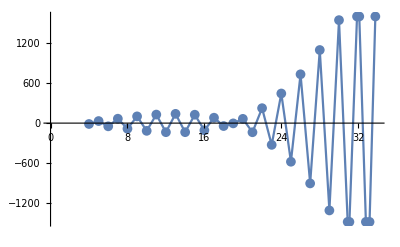

```mathematica
ListLinePlot[Table[
With[
{g=MinimalGraph[k]},
{VertexCount[g],Vals2[g][[4]]}
],{k,3,33}],PlotMarkers->{Automatic, 10}]
```

```mathematica
Differences[Table[
With[
{g=MinimalGraph[k]},
TrianglesInGraph[g]
],{k,2,30,2}]]
```

{6,5,7,6,6,6,6,5,6,7,6,5,6,7}

```mathematica
FindFundamentalCycles[]
```

```mathematica
TableForm[Table[
With[
{g=MinimalGraph[k]},
{VertexCount[g],
EdgeCount[g],
FindFundamentalCycles[g]//Length,
FindFundamentalCycles[EdgeDelete[g,1<->2]]//Length,
ChromaticPolynomial[EdgeDelete[g,1<->2],4]/24-1
}
],{k,3,10}],
TableHeadings->{None, {"v","edges","cycles+","cycles-","colofour"}},TableDepth->2]
```

v | edges | cycles+ | cycles- | colofour
4 | 6 | 3 | 2 | 1
5 | 9 | 5 | 4 | 2
6 | 12 | 7 | 6 | 4
7 | 15 | 9 | 8 | 8
8 | 18 | 11 | 10 | 16
9 | 21 | 13 | 12 | 32
10 | 24 | 15 | 14 | 64
11 | 27 | 17 | 16 | 128

```mathematica
TableForm[Table[
With[
{g=MinimalGraph[k]},
{VertexCount[g],
EdgeCount[g],
FindCycle[g]//Length,
FindFundamentalCycles[EdgeDelete[g,1<->2]]//Length,
ChromaticPolynomial[EdgeDelete[g,1<->2],4]/24-1
}
],{k,3,10}],
TableHeadings->{None, {"v","edges","cycles+","cycles-","colofour"}},TableDepth->2]
```

```mathematica
TableForm[Table[
With[
{g=JacobsThalGraph[k]},
{VertexCount[g],
EdgeCount[g],
FindFundamentalCycles[g]//Length,
FindFundamentalCycles[EdgeDelete[g,1<->2]]//Length,
ChromaticPolynomial[EdgeDelete[g,1<->2],4]/24-1
}
],{k,1,10}],
TableHeadings->{None, {"v","edges","cycles+","cycles-","colofour"}},TableDepth->2]
```

v | edges | cycles+ | cycles- | colofour
5 | 9 | 5 | 4 | 2
6 | 12 | 7 | 6 | 4
7 | 15 | 9 | 8 | 8
8 | 18 | 11 | 10 | 16
9 | 21 | 13 | 12 | 32
10 | 24 | 15 | 14 | 64
11 | 27 | 17 | 16 | 128
12 | 30 | 19 | 18 | 256
13 | 33 | 21 | 20 | 512
14 | 36 | 23 | 22 | 1024